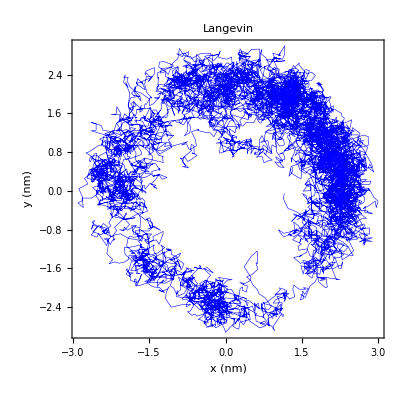

```mathematica
data=Import["~/Dropbox/Teaching/Github/PHYS6328-Python/4-external_forces/trajectory_langevin.txt","csv"];
ListPlot[Transpose[Delete[Transpose[data],1]],
PlotRange->All,
AspectRatio->1,
Joined->True,
PlotStyle->{Blue,Thickness[.001]},
Frame->True,Axes->False,
PlotLabel->"Langevin",
FrameLabel->{"x (nm)","y (nm)"}
]
```

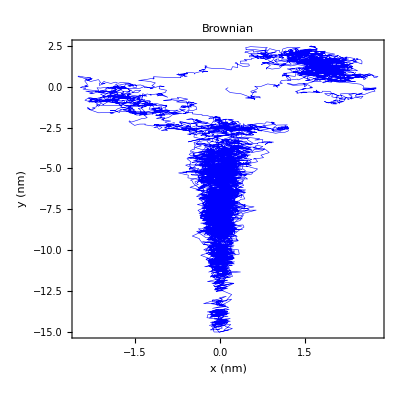

```mathematica
data=Import["~/Dropbox/Teaching/Github/PHYS6328-Python/4-external_forces/trajectory_overdamped.txt","csv"];
ListPlot[Transpose[Delete[Transpose[data],1]],
PlotRange->All,
AspectRatio->1,
Joined->True,
PlotStyle->{Blue,Thickness[.001]},
Frame->True,Axes->False,
PlotLabel->"Brownian",
FrameLabel->{"x (nm)","y (nm)"}
]
```